```mathematica
(*Mathematica*)
```

```mathematica
Clear[t,a,p,aa,bb]
(* cf: A073058*)
(* F. M. Dekking, "Recurrent Sets" ,Advances in Mathematics,vol. 44, no.1,April 1982, page 85, section 4.15*)
CompanionMatrix[p_, x_] := Module[{cl=CoefficientList[p, x], deg, m}, cl=Drop[cl/Last[cl], -1]; deg=Length[cl]; If[deg==1, {-cl}, m=RotateLeft[IdentityMatrix[deg]]; m[[ -1]]=-cl; Transpose[m]]]; 
m=Transpose[CompanionMatrix[(x^3-x^2-x-1)*(x^2+x+1),x] ]
```

{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{1,2,3,1,0}}

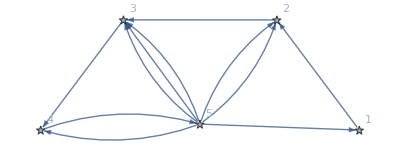

```mathematica
AdjacencyGraph[m,VertexLabels->"Name",ImageSize->Full,VertexShapeFunction->"Star"]
```

```mathematica
(* 5 symbol  *)
```

```mathematica
n0=9
```

9

```mathematica
(* substitution *)
```

```mathematica
s[1]={2,0,0,0,0,0,0,0}; s[2]={3,0,0,0,0,0,0,0}; s[3]={4,0,0,0,0,0,0,0}; s[4]={5,0,0,0,0,0,0,0,0};s[5]={1,2,2,3,3,3,4,0,0};
```

```mathematica
(* make matrix*)
```

```mathematica
M=Table[Table[Count[s[j],i],{i,1,5}],{j,1,5}]
```

{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{1,2,3,1,0}}

```mathematica
AdjacencyGraph[M,VertexLabels->"Name",ImageSize->Full,VertexShapeFunction->"Star"]
```

-Graphics-

```mathematica
(* make polynomial*)
```

```mathematica
Det[M-x*IdentityMatrix[5]]
```

1+2 x+3 x^2+x^3-x^5

```mathematica
x/.NSolve[CharacteristicPolynomial[M,x]==0,x]
```

{-0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ,-0.419643-0.606291 ⅈ,-0.419643+0.606291 ⅈ,1.83929}

```mathematica
Abs[%]
```

{1.,1.,0.737353,0.737353,1.83929}

```mathematica
z=x/.NSolve[CharacteristicPolynomial[M,x]==0,x][[3]]
```

-0.419643-0.606291 ⅈ

```mathematica
Abs[%]
```

0.737353

```mathematica
Clear[s,p]
```

```mathematica
(* program to express the substitution *)
```

```mathematica
Clear[s,t,p]
```

```mathematica
s[1]={2}; s[2]={3}; s[3]={4}; s[4]={5};s[5]={1,2,2,3,3,3,4};
```

```mathematica
t[a_] :=Flatten[s/@a];
```

```mathematica
w=Flatten[Table[s[i],{i,5}]]
```

{2,3,4,5,1,2,2,3,3,3,4}

```mathematica
p[0]={1};p[1]=t[p[0]];
```

```mathematica
p[n_]:=t[p[n-1]]
```

```mathematica
aa=p[25];
```

```mathematica
Length[aa]
```

867985

```mathematica
(* graphing subroutine*)
```

```mathematica
x/.NSolve[CharacteristicPolynomial[M,x]==0,x][[3]]
```

-0.419643-0.606291 ⅈ

```mathematica
v=Table[N[{Re[z^i],Im[z^i]}],{i,5}]
```

{{-0.419643,-0.606291},{-0.191488,0.508852},{0.388869,-0.097439},{-0.222263,-0.194878},{-0.0248817,0.216535}}

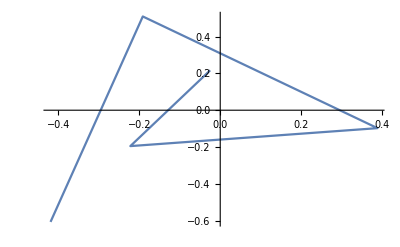

```mathematica
ListLinePlot[v]
```

```mathematica
bb=aa/. 1->v[[1]]/. 2->v[[2]]/. 3->v[[3]]/. 4->v[[4]]/. 5->v[[5]];
```

```mathematica
cc=FoldList[Plus,{0,0},bb];
```

```mathematica
g0=ListPlot[cc,PlotRange->All,Axes->False,ImageSize->{2000,2000},PlotStyle->{PointSize[0.001]},ColorFunction->Hue];
```

```mathematica
allColors=ColorData["Legacy"][[3,1]];
firstCols={"Cyan","ManganeseBlue","Blue","DodgerBlue","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
dd=Flatten[ParallelTable[{PointSize[0.001],cols[[aa[[n]]]],Point[cc[[n]]]},{n,Min[Length[cc],Length[aa]]}]];
```

```mathematica
g1=Show[Graphics[dd],ImageSize->{2000,2000},Background->Black];
```

```mathematica
Export["5Symbol_4th_cubic_rootpowers_level25_1_.jpg",g0]
```

5Symbol_2nd_cubic_rootpowers_level31_1_Startvector.jpg

```mathematica
Export["5Symbol_4th_cubic_rootpowers_level25_2_.jpg",g1]
```

5Symbol_2nd_cubic_rootpowers_level31_2_Startvector.jpg

```mathematica
Export["5Symbol_4th_cubic_rootpowers_level25_3_.jpg",GraphicsGrid[{{g0},{g1}},ImageSize->{2000,4000}]]
```

5Symbol_2nd_cubic_rootpowers_level31_3_Startvector.jpg

```mathematica
(*Export["5Symbol_cycle5_Pentagon_level16_ReverseStartvector.jpg",GraphicsGrid[{{g0},{g1}},ImageSize->{2000,4000}]]*)
```

```mathematica
(*end*)
```